```mathematica
(*Import findLinksPackage*)
AppendTo[$Path,NotebookDirectory[]];
Needs["findLinksPackage`"];
```

```mathematica
(*maxnIL graph of order 6*)
```

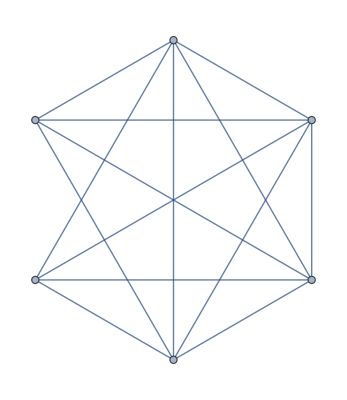
```mathematica
(*K_6-e*)
G=-Graphics-;
upEdges={6<->3,1<->2}; 
rightEdges={4<->6,4<->2};
findLinks[G, upEdges, rightEdges];
```

```mathematica
(*maxnIL graphs of order 7*)
```

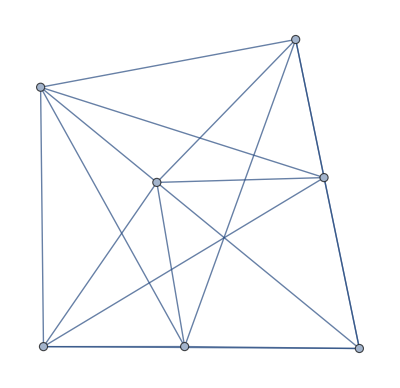
```mathematica
(*7_1*)
G=-Graphics-;
upEdges={2<->5,2<->3,6<->3,6<->1}; 
rightEdges={6<->2,4<->2,4<->5,1<->5};
findLinks[G, upEdges, rightEdges];
```

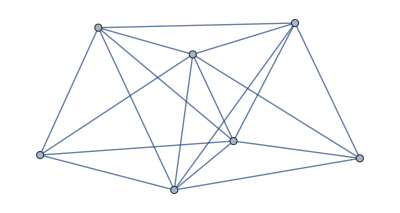
```mathematica
(*7_2*)
G=-Graphics-;
upEdges={5<->2,5<->3,5<->7,4<->7,4<->2}; 
rightEdges={4<->5,6<->5,6<->3,2<->5};
findLinks[G, upEdges, rightEdges];
```

```mathematica
(*maxnIL graphs of order 8*)
```

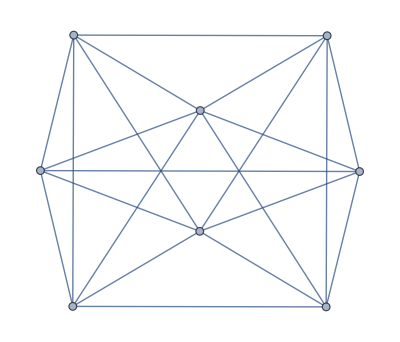
```mathematica
(*8_1*)
G=-Graphics-;
upEdges={2<->6,7<->6,7<->3,5<->3}; 
rightEdges={5<->2,5<->8,1<->8,3<->8,3<->6};
findLinks[G, upEdges, rightEdges];
```

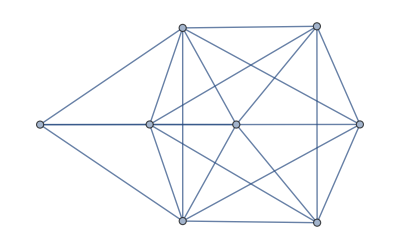
```mathematica
(*8_2*)
G=-Graphics-;
upEdges={8<->4,8<->6,8<->1,3<->1,7<->1,7<->4}; 
rightEdges={7<->8,2<->8,2<->6,4<->6,4<->8};
findLinks[G, upEdges, rightEdges];
```

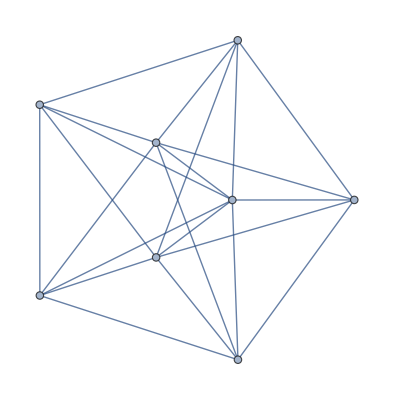
```mathematica
(*8_3*)
G=-Graphics-;
upEdges={7<->5,3<->5,3<->6,1<->6}; 
rightEdges={1<->7,4<->7,4<->2,6<->2};
findLinks[G, upEdges, rightEdges];
```

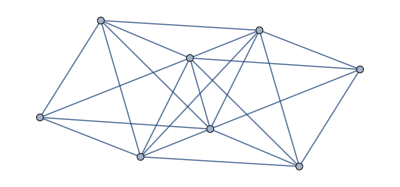
```mathematica
(*8_4*)
G=-Graphics-;
upEdges={5<->8,5<->3,1<->3,1<->8,6<->8}; 
rightEdges={6<->5,6<->2,4<->2,8<->2,8<->5};
findLinks[G, upEdges, rightEdges];
```

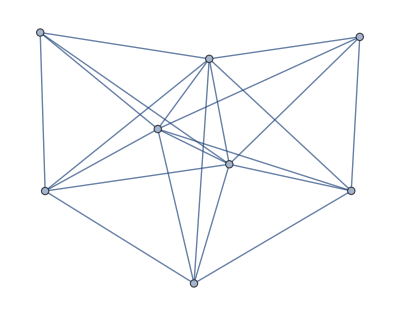
```mathematica
(*8_5*)
G=-Graphics-;
upEdges={2<->8,7<->3,7<->5,7<->8,4<->8}; 
rightEdges={4<->2,4<->6,1<->6,8<->6,8<->3,8<->2};
findLinks[G, upEdges, rightEdges];
```

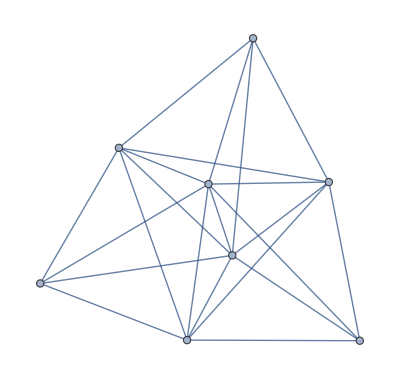
```mathematica
(*8_6*)
G=-Graphics-;
upEdges={1<->5,4<->5,4<->6,8<->6,8<->3,8<->5}; 
rightEdges={8<->5,8<->1,8<->7,2<->7,3<->7,3<->5};
findLinks[G, upEdges, rightEdges];
```

```mathematica
(*maxnIL graphs of order 9*)
```

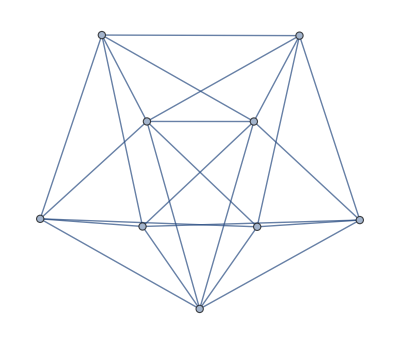
```mathematica
(*9_1*)
G=-Graphics-;
upEdges={7<->5,1<->3,4<->8}; 
rightEdges={4<->8,4<->7,4<->2,6<->2,6<->8,3<->8};
findLinks[G, upEdges, rightEdges];
```

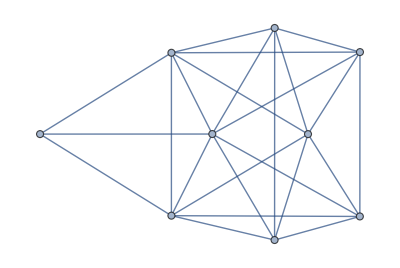
```mathematica
(*9_2*)
G=-Graphics-;
upEdges={2<->7,9<->7,9<->5,9<->3,6<->3}; 
rightEdges={6<->4,8<->4,8<->7,3<->7};
findLinks[G, upEdges, rightEdges];
```

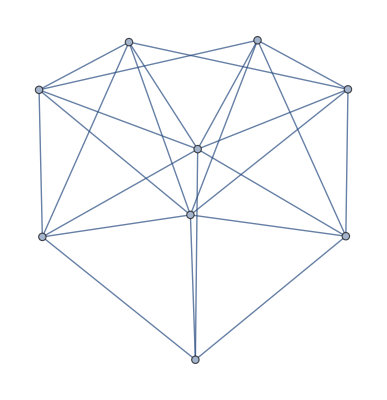
```mathematica
(*9_3*)
G=-Graphics-;
upEdges={1<->8,7<->8,2<->8,2<->6,4<->6,4<->8}; 
rightEdges={4<->8,4<->1,9<->1,9<->5};
findLinks[G, upEdges, rightEdges];
```

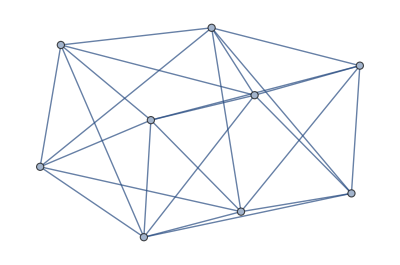
```mathematica
(*9_5*)
G=-Graphics-;
upEdges={5<->2,5<->9,5<->7,1<->7,8<->2}; 
rightEdges={8<->5,8<->3,4<->9,2<->9,2<->5};
findLinks[G, upEdges, rightEdges];
```

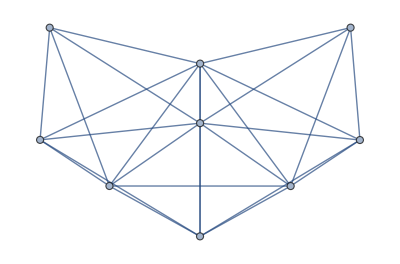
```mathematica
(*9_8*)
G=-Graphics-;
upEdges={2<->6,2<->7,9<->7,9<->2,9<->1,9<->6,4<->6}; 
rightEdges={4<->2,8<->2,8<->3,8<->7,6<->7,6<->2};
findLinks[G, upEdges, rightEdges];
```

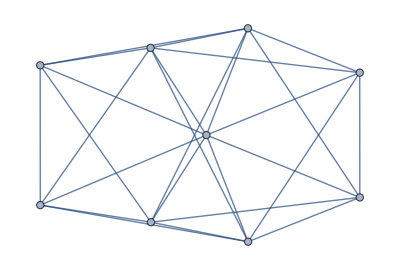
```mathematica
(*9_9*)
G=-Graphics-;
upEdges={1<->6,1<->7,9<->7,9<->4,9<->6,3<->6}; 
rightEdges={3<->1,3<->5,8<->5,6<->7,6<->1};
findLinks[G, upEdges, rightEdges];
```

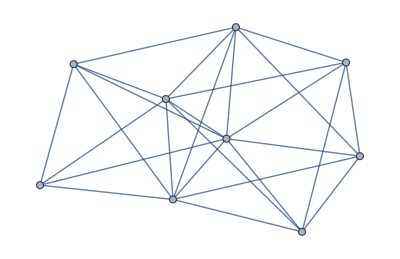
```mathematica
(*9_11*)
G=-Graphics-;
upEdges={5<->1,9<->1,9<->2,9<->6,3<->6,3<->1}; 
rightEdges={3<->1,3<->5,8<->5,8<->7,6<->7,6<->1};
findLinks[G, upEdges, rightEdges];
```

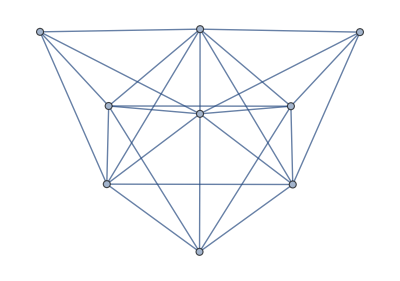
```mathematica
(*9_12*)
G=-Graphics-;
upEdges={1<->5,7<->5,7<->3,7<->8,4<->8}; 
rightEdges={4<->1,4<->6,2<->6,8<->6,8<->5};
findLinks[G, upEdges, rightEdges];
```

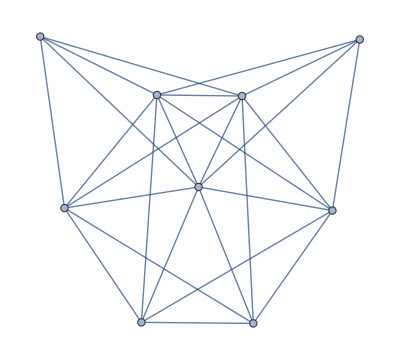
```mathematica
(*9_13*)
G=-Graphics-;
upEdges={8<->7,8<->5,4<->5,4<->1,6<->1,6<->7}; 
rightEdges={6<->8,3<->8,7<->2,7<->5,7<->8};
findLinks[G, upEdges, rightEdges];
```

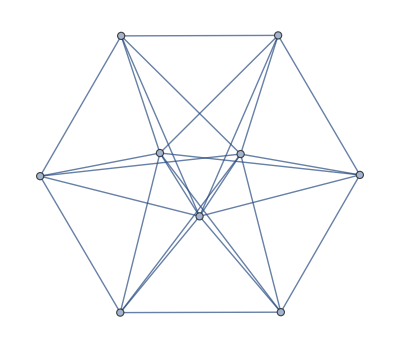
```mathematica
(*9_14*)
G=-Graphics-;
upEdges={8<->6,8<->3,5<->3,5<->7,1<->7}; 
rightEdges={1<->8,4<->8,4<->2,7<->2,7<->6};
findLinks[G, upEdges, rightEdges];
```

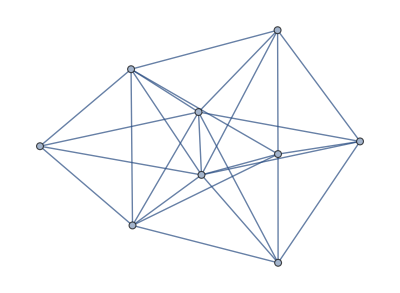
```mathematica
(*9_15*)
G=-Graphics-;
upEdges={8<->6,8<->3,5<->3,5<->7,1<->7}; 
rightEdges={1<->8,4<->8,4<->2,4<->6,7<->6};
findLinks[G, upEdges, rightEdges];
```

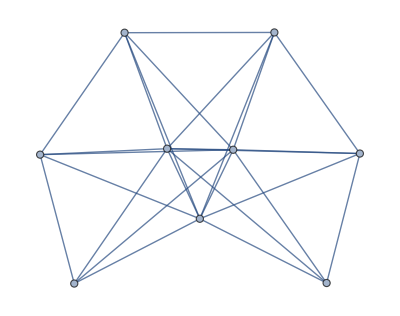
```mathematica
(*9_16*)
G=-Graphics-;
upEdges={8<->7,8<->6,8<->2,5<->2,5<->7,1<->7}; 
rightEdges={1<->8,4<->8,7<->3,7<->6,7<->8};
findLinks[G, upEdges, rightEdges];
```

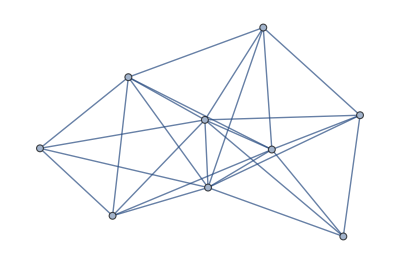
```mathematica
(*9_17*)
G=-Graphics-;
upEdges={9<->8,9<->4,9<->6,2<->6,2<->8,5<->8}; 
rightEdges={5<->9,3<->9,8<->1,8<->4,8<->9};
findLinks[G, upEdges, rightEdges];
```

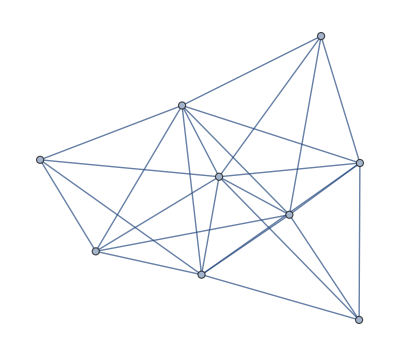
```mathematica
(*9_18*)
G=-Graphics-;
upEdges={2<->9,5<->9,7<->9,7<->4,7<->1}; 
rightEdges={7<->1,7<->2,7<->6,8<->6,8<->1,5<->1};
findLinks[G, upEdges, rightEdges];
```

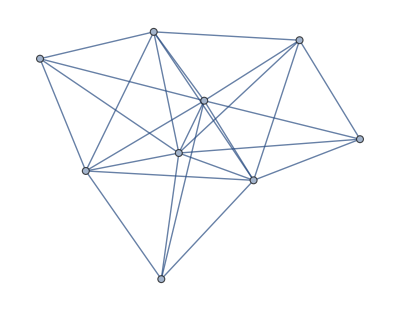
```mathematica
(*9_19*)
G=-Graphics-;
upEdges={8<->7,8<->5,8<->3,4<->7,1<->7}; 
rightEdges={1<->8,6<->8,6<->2,6<->5,7<->5,7<->8};
findLinks[G, upEdges, rightEdges];
```

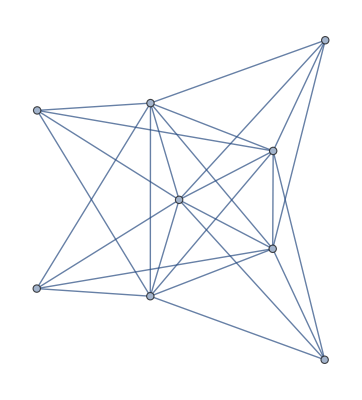
```mathematica
(*9_20*)
G=-Graphics-;
upEdges={6<->8,6<->7,6<->4,2<->8,5<->8}; 
rightEdges={5<->6,5<->1,5<->7,3<->7,8<->7,8<->6};
findLinks[G, upEdges, rightEdges];
```

```mathematica
(*non-maxnIL MTN graphs of order 9*)
```

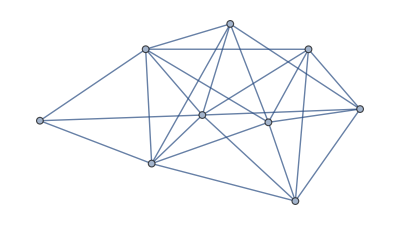
```mathematica
(*NTS_9_1*)
G=-Graphics-;
upEdges={3<->9,5<->9,2<->6,2<->4,2<->9}; 
rightEdges={2<->9,8<->7,4<->7,4<->9};
findLinks[G, upEdges, rightEdges];
```

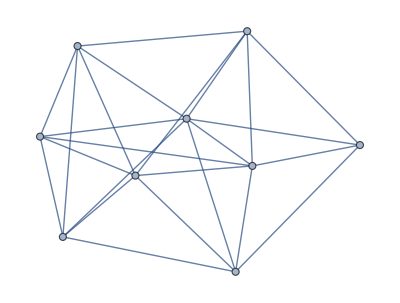
```mathematica
(*NTS_9_2*)
G=-Graphics-;
upEdges={1<->8,1<->7,3<->7,3<->5,6<->8}; 
rightEdges={6<->1,6<->4,2<->4,8<->4,8<->7,8<->1};
findLinks[G, upEdges, rightEdges];
```

No links found.

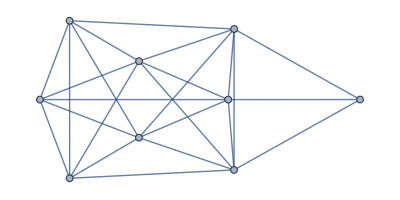
```mathematica
(*NTS_9_3*)
G=-Graphics-;
upEdges={6<->4,6<->2,6<->8,1<->8}; 
rightEdges={7<->9,4<->9,4<->2,4<->6};
findLinks[G, upEdges, rightEdges];
```

No links found.

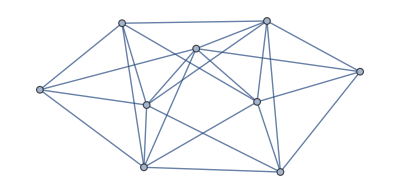
```mathematica
(*NTS_9_4*)
G=-Graphics-;
upEdges={5<->3,5<->1,5<->7,2<->7,1<->7,1<->3}; 
rightEdges={1<->5,1<->8,6<->8,6<->9,3<->9,3<->5};
findLinks[G, upEdges, rightEdges];
```

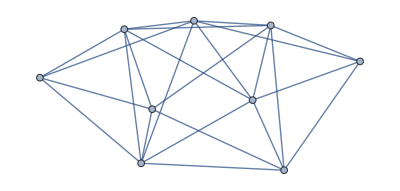
```mathematica
(*NTS_9_5*)
G=-Graphics-;
upEdges={9<->8,9<->4,9<->2,5<->2,5<->8}; 
rightEdges={5<->8,5<->3,5<->1,7<->1,2<->8};
findLinks[G, upEdges, rightEdges];
```

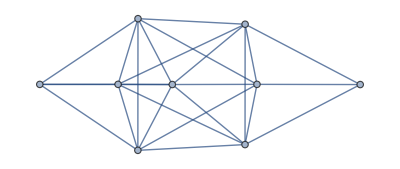
```mathematica
(*NTS_9_6*)
G=-Graphics-;
upEdges={6<->8,6<->4,6<->1,1<->9,1<->8}; 
rightEdges={1<->6,5<->2,8<->2,8<->4,8<->6};
findLinks[G, upEdges, rightEdges];
```

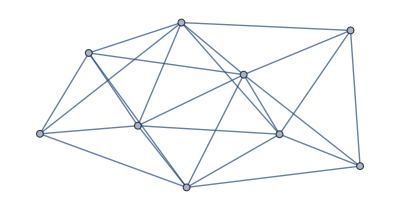
```mathematica
(*NTS_9_7*)
G=-Graphics-;
upEdges={5<->3,5<->8,6<->8,6<->2,6<->4,9<->4}; 
rightEdges={9<->5,9<->1,3<->1,3<->8,3<->5};
findLinks[G, upEdges, rightEdges];
```

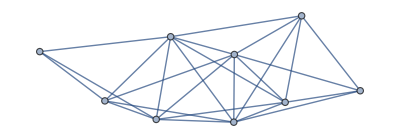
```mathematica
(*NTS_9_8*)
G=-Graphics-;
upEdges={9<->7,9<->1,9<->6,2<->6,2<->4,2<->7}; 
rightEdges={3<->9,3<->5,3<->1,7<->1,7<->9};
findLinks[G, upEdges, rightEdges];
```

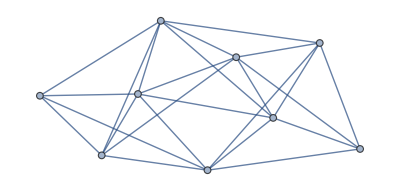
```mathematica
(*NTS_9_9*)
G=-Graphics-;
upEdges={7<->1,7<->6,4<->6,4<->9,3<->9,3<->1}; 
rightEdges={3<->7,8<->7,8<->2,8<->6,1<->6,1<->7};
findLinks[G, upEdges, rightEdges];
```

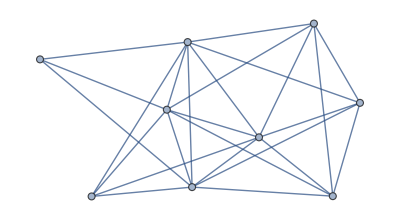
```mathematica
(*NTS_9_10*)
G=-Graphics-;
upEdges={5<->9,7<->2,7<->9,1<->9}; 
rightEdges={1<->5,3<->5,3<->8,9<->8,9<->2,9<->5};
findLinks[G, upEdges, rightEdges];
```

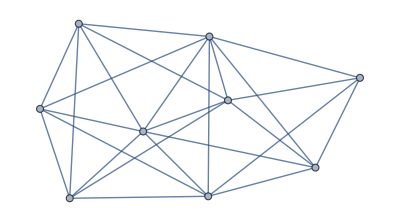
```mathematica
(*NTS_9_11*)
G=-Graphics-;
upEdges={5<->1,3<->1,3<->6,8<->6,8<->5}; 
rightEdges={8<->5,8<->7,2<->7,4<->7};
findLinks[G, upEdges, rightEdges];
```